Spot Assay Processor

The Mathematica “Spot Assay Processor” notebook is designed to quantify cell growth on solid media plates incubated under the influence of different environmental factors. It does so by measuring the size of the colonies formed by the growing cells in pictures taken from the solid media plate with colonies at regular intervals. The colonies are laid out on a grid using a “spotting” technique commonly having rows for the different strains or mutants of the organisms under study and a dilution series as columns.

The notebook processes these images in the following successive steps:

Detect colonies on the background using a sequence of image processing techniques:

Convert the image to a grayscale representation.

Tophat Transform filter to equalize possible uneven illumination in the image. Uses tophatr variable as threshold.

Threshold filter to better define colonies and boundaries between colony and medium. This filter uses cluster variance maximization (Otsu’s algorithm) to perform automatic clustering-based image thresholding on grayscale images.

Binarization to convert the pixels of the detected colonies to 1 (white) and background pixels to 0 (black).

Isolate the colonies in the image by partitioning the image into a equally spaced grid according to the imagegrid variable (columns x rows). The partitioning scheme uses soft boundaries to ensure that each partition is of equal pixels size and compensate for minor misalignment of colonies in the grid cells. The latter prevents the edges of one colony to flow over into the grid cell of another colony leading to false positives in colony pixel counts.

Count the 1’s in the binary matrices after partitioning as a metric for colony growth.

In case of a reference plate, the pixel counts in the assay are normalized by the pixel counts in the reference. This may lead the less pixels than the reference image in which case the organism/cell growth rate is reduced (sensitivity) under influence of the environmental factor, no effect or more pixels in which case colony growth in increased under influence of the environmental factor. This notebook focuses on sensitivity and therefor all pixel counts higher than the control are set to equal the control (growth cannot be higher than the control).

In case of a control image, a final value for sensitivity is calculated by averaging the difference in growth over the dilution series.

```mathematica
Program usage
```

The interactive notebook will ask you to define one or multiple image files to process and optionally a reference image. You can test the script by using the test images shipped with the software (condition-x.png and the reference image control.png). Mathematica will handle most common image file formats automatically.

Of the 3 program parameters you can set (imagegrid, padding and tophatr), the imagegrid needs to match the grid layout of the colonies in your image as columns x rows. For the test images you need to set this parameter to {4, 12}. Please note that all the images you process in one run of the script need to have the same grid layout.

The program outputs a bar graph with a sensitivity value between 0 and 1 for every row in each of the images you supplied. In addition the sensitivity data for all images are exported to an Excel .xls file names “spottingdata.xls” by default in the same location as where the spot_assay_processor.nb notebook is located. The path to this file is defined in the outputexcelpath variable.

Program settings

Import::chtype: First argument $Canceled is not a valid file, directory, or URL specification.

ColorConvert::ccvinput: $Failed should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

TopHatTransform::arg1: The first argument ColorConvert[$Failed,Grayscale] is neither a rectangular array nor an image.

Threshold::wlist: Argument TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr] should be one of rectangular array of any depth, image, sound, or sampled sound list.

Binarize::imginv: Expecting an image or graphics instead of Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}].

ImageDimensions::imginv: Expecting an image or graphics instead of Binarize[Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}]].

ImagePartition::imginv: Expecting an image or graphics instead of Binarize[Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}]].

ImageData::imginv: Expecting an image or graphics instead of Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}].

Binarize::imginv: Expecting an image or graphics instead of 0.

ImageData::imginv: Expecting an image or graphics instead of 1/4 ImageDimensions[Binarize[Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}]]].

ImageData::imginv: Expecting an image or graphics instead of 1/12 ImageDimensions[Binarize[Threshold[TopHatTransform[ColorConvert[$Failed,Grayscale],tophatr],{Hard,Cluster}]]].

General::stop: Further output of ImageData::imginv will be suppressed during this calculation.

ImagePartition::imginv: Expecting an image or graphics instead of Binarize[0].

$Canceled

False

ImagePartition[Binarize[0],{0,0},0→0]

Binarize::imginv: Expecting an image or graphics instead of 0..

ImagePartition::imginv: Expecting an image or graphics instead of Binarize[0.].

Binarize::imginv: Expecting an image or graphics instead of 0..

ImagePartition::imginv: Expecting an image or graphics instead of Binarize[0.].

Binarize::imginv: Expecting an image or graphics instead of 0..

General::stop: Further output of Binarize::imginv will be suppressed during this calculation.

ImagePartition::imginv: Expecting an image or graphics instead of Binarize[0.].

General::stop: Further output of ImagePartition::imginv will be suppressed during this calculation.

/Users/mvdijk/Desktop/angelina/spot-assay-processor/condition-1.png

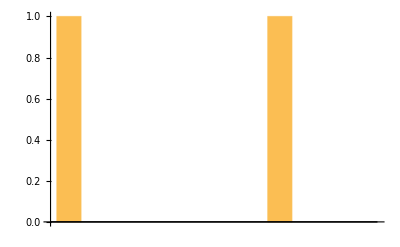

/Users/mvdijk/Desktop/angelina/spot-assay-processor/condition-2.png

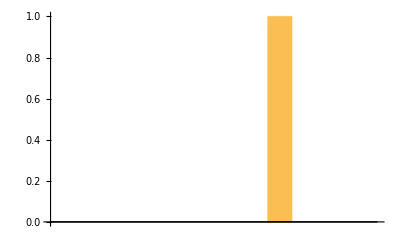

```mathematica
imagegrid={4,12};
padding = 0.2;
tophatr = 20;

(*SELECTING FILES*)
imagepaths =  SystemDialogInput["FileOpen", WindowTitle->"Select one or multiple image files"];
controlimagepath = SystemDialogInput["FileOpen", WindowTitle->"Select a control image"];
outputexcelpath = FileNameJoin[{NotebookDirectory[], "spottingdata.xls"}];

(*ensure controle image paths is one path, and imagepaths is a list*)
controlimagepath = First[List[controlimagepath]];
imagepaths = Flatten[List[imagepaths]];

(*FUNCTIONS*)
(*Count all pixels not black (0)*)
CountWhite = Function[i,Count[Flatten[ImageData@i],x_/;x>0.]];

(*pre-process image: remove uneven field illumination, binarize image*)
ProcessImage = Function[img,
Binarize[Threshold[TopHatTransform[ColorConvert[img, "Grayscale"],tophatr], {"Hard","Cluster"}]]
];

(*Partition image and count white pixels*)
imagegrid[[2]] - padding;  (*apply bit of padding to the column height*)
PartitionAndCount= Function[img,
Map[CountWhite, ImagePartition[img,ImageDimensions[img]/imagegrid, Padding->Black ], {2}]
];

(*Replace all values largen than 0 by 0*)
PositiveReplace[x_]:=If[x>0,0,x];
SetAttributes[PositiveReplace,Listable];

(*MAIN ROUTINE*)
(*Import and process control image file*)
nocontrol = controlimagepath === "$Canceled";
controlcount = If[nocontrol, 0, PartitionAndCount[ProcessImage[Import[controlimagepath]]]];

collecteddata = {};
For[i=1,i≤Length[imagepaths ],i++,
assay = ProcessImage[Import[imagepaths [[i]]]];

(*Partition image and count white pixels*)
assaycount = PartitionAndCount[assay];

(*Normalize assay dilution series with respect control dilution series
if there is a control image defined*)
If[nocontrol,whitecount = assaycount, whitecount = (assaycount-controlcount)/controlcount];

(*Replace all normalized count differces larger than 0 by 0. For sensitivity data, growth should not be more than control*)
whitecount =PositiveReplace[whitecount];

(*Average of absolute values in the series. If 0 than case not sensitive for condition
if 1 then fully sensitive (no growth)*)
sensitivity = N[Abs[(Map[Total,whitecount,{1}])/imagegrid[[1]]]];
AppendTo[collecteddata, sensitivity];
Print[imagepaths [[i]]];
Print[BarChart[sensitivity]];
]

collecteddata = Transpose[collecteddata];
filenames = Map[FileBaseName, imagepaths ];
Export[outputexcelpath,PrependTo[collecteddata, filenames], "XLS"];
```